## Numerical Analysis — Problem Set 8 — Probability Distributions

## Due Tuesday, Nov. 8 (beginning of class) In this problem set, you will study two simple and important probability distributions, the uniform distribution, the binomial distribution, which is an approximation to the Gaussian distribution (colloquially known as the bell curve).

### 1. The Uniform Distribution

(a) Look at the random number generation program on p. 116 of the HP-25 Applications Programs book. Modify it so that after step 07, where the number is stored, the number is multiplied by 8, then add 0.5 to it, and then call f INT. The last two steps round the number to the nearest integer. None of these modifications change what is stored in R0. They only change what is displayed to be an integer between 0 and 8.

You don’t need to turn this program in.

So that we all get the same answer in what follows, let’s all start with u_0=0.1917.

(b) Run the program 25 times. Fill out the following table:

```mathematica
MatrixForm[Transpose[Table[{i, "  "}, {i, Range[1, 25, 1]}]]]
```

(1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25
   |    |    |    |    |    |    |    |    |    |    |    |    |    |    |    |    |    |    |    |    |    |    |    |   )

(c) Google the word “histogram” and look at a few of the images so that you know what you are trying to create. Create a histogram of the above data by first filling in the following table with tally marks:

  In case, you don’t know, what is on the left are tally marks. It is just a convenient way of counting.

```mathematica
MatrixForm[Transpose[Table[{i, "      "}, {i, Range[0, 8, 1]}]]]
```

I have done the first few.

(0 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8
       |        |        |        |        |        |        |        |       )

Now plot the data:

```mathematica
Histogram[{},9, PlotRange->{{-0.5, 8.5},{0, 9}}, Ticks->{Range[0, 9, 1], Range[0, 9, 1]}]
```

-Graphics-

(d) There were 25 data points in total. The sum of all the histogram bins is 25. Create a normalized histogram by dividing each of the values in part (c) by 25.

(0 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8
       |        |        |        |        |        |        |        |       )

Plot those values:

```mathematica
Histogram[{},9, PlotRange->{{-0.5, 8.5},{0, 0.36}}, Ticks->{Range[0, 9, 1], Range[0, 0.36, 0.04]}]
```

-Graphics-

This is called a normalized histogram because the sum of all the bins is 1.0.

Discussion: you have made something that if you had done it hundreds or thousands of times would slowly become the uniform distribution. The value in each bin would become closer and closer to 0.111.

### 2. The Binomial Distribution

(a) Go back to the original program on p. 116. Modify the program — this won’t be as easy as in 1(a)! — to generate 8 random numbers between 0 and 1 and sum them up. Then, add 0.5 to the sum and call f INT. This will also generate a number between 0 and 8.

Turn this program in on one of the HP-25 Program Forms.

Again, so that we all get the same answer in what follows, start with u_0=0.1917.

(b) Run the program 25 times. Fill out the following table.

```mathematica
MatrixForm[Transpose[Table[{i, "  "}, {i, Range[1, 25, 1]}]]]
```

(1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25
   |    |    |    |    |    |    |    |    |    |    |    |    |    |    |    |    |    |    |    |    |    |    |    |   )

(c) Create a histogram of this data by filling in the following table with tally marks:

```mathematica
MatrixForm[Transpose[Table[{i, "      "}, {i, Range[0, 8, 1]}]]]
```

(0 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8
       |        |        |        |        |        |        |        |       )

```mathematica
Histogram[{},9, PlotRange->{{-0.5, 8.5},{0, 9}}, Ticks->{Range[0, 8, 1], Range[0, 9, 1]}]
```

-Graphics-

(d) Create a normalized histogram by dividing each of the values in part (c) by 25.

(0 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8
       |        |        |        |        |        |        |        |       )

Plot those values:

```mathematica
Histogram[{},9, PlotRange->{{-0.5, 8.5},{0, 0.36}}, Ticks->{Range[0, 8, 1], Range[0, 0.36, 0.04]}]
```

-Graphics-

Discussion: you have made something that if you had done it hundreds or thousands of times would slowly become the binomial distribution. Here is what you would get if you did it so many times that the non-uniformities smoothed out. Please ignore all the jiggering I had to do to get a nice-looking plot and just look at the plot below.

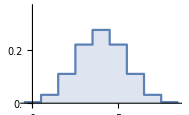

```mathematica
n = Table[{i-0.5, N[Binomial[8, i]/2^8]},{i, 0, 8}];n2 = Table[{i+0.5, N[Binomial[8, i]/2^8]},{i, 0, 8}];woven = Flatten[Transpose[{n, n2}], 1]; ListLinePlot[woven, PlotRange->{{-0.5, 8.5},{0, 0.36}}, Ticks->{Range[0, 8, 1], Range[0, 0.36, 0.04]}, Filling->Axis]
```

I hope you can see the classic bell curve emerging:

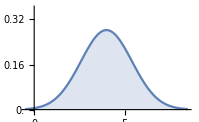

```mathematica
Plot[PDF[NormalDistribution[4,Sqrt[2]], x]//Evaluate, {x, -0.5, 8.5},PlotRange->{{-0.5, 8.5},{0, 0.36}}, Ticks->{Range[0, 8, 1], Range[0, 0.36, 0.04]}, Filling->Axis]
```